### Basic:

```mathematica
FNJ=FileNameJoin;
```

```mathematica
RelativeDir[dir_]:=FileNameJoin[{NotebookDirectory[],dir}]
```

```mathematica
Replicate[list_,n_]:=Flatten[Transpose[ConstantArray[list,n]]]
```

```mathematica
ToText[list_]:=StringJoin[Riffle[ToString[#]&/@list,"\n"]]
```

```mathematica
ShiftLeft[list_,n_]:=Drop[PadLeft[list,Length[list]+n],-n]
```

```mathematica
ShiftRight[list_,n_]:=Drop[PadRight[list,Length[list]+n],n]
```

```mathematica
Half[list_]:= Take[list, Floor[Length[list]/2]]
```

### Before simulation:

```mathematica
(*-------parameters-------*)
td = 3; blocks = 4; l = 100;
(*------------------------*)
data=RandomInteger[{-16,16},l];
ker = RandomInteger[{-16,16},td*blocks];
upKer = RandomInteger[{-16,16},td*6];
```

```mathematica
expected=ListConvolve[Reverse[ker],data,1,0];
```

```mathematica
Max[Abs[expected]]
```

806

```mathematica
Export[RelativeDir["data.dat"],ToText[Replicate[data,td]]];Export[RelativeDir["coefs.dat"],ToText[ker]];Export[RelativeDir["upsamp_coefs.dat"],ToText[upKer]];
```

### After simulation:

```mathematica
ker
```

{-6,4,-13,5,-11,-9,-8,-8,13,-1,4,-10}

```mathematica
expected
```

{20,22,-150,173,67,172,-86,-189,300,-235,402,23,659,411,-164,140,-206,365,236,206,-100,-269,-287,196,81,-145,-444,-433,-221,-7,241,-232,-333,-386,-162,266,-186,167,-121,51,59,-98,26,-576,-76,-100,156,105,-126,54,-127,-329,2,-434,160,-387,-198,-425,-395,335,-66,450,-608,240,-255,375,-151,87,-117,-36,253,-319,249,-555,110,-338,167,-189,-217,-258,62,463,541,-124,195,-143,581,239,-90,107,-85,806,-91,290,-110,312,548,19,-3,14}

```mathematica
upKer
```

{1,1,-13,1,-8,11,9,12,-6,11,12,10,13,16,-10,-14,-6,-2}

```mathematica
Max[lol]
```

lol

```mathematica
upIn=Flatten@Riffle[expected,{ConstantArray[0,2]}]
```

{20,0,0,22,0,0,-150,0,0,173,0,0,67,0,0,172,0,0,-86,0,0,-189,0,0,300,0,0,-235,0,0,402,0,0,23,0,0,659,0,0,411,0,0,-164,0,0,140,0,0,-206,0,0,365,0,0,236,0,0,206,0,0,-100,0,0,-269,0,0,-287,0,0,196,0,0,81,0,0,-145,0,0,-444,0,0,-433,0,0,-221,0,0,-7,0,0,241,0,0,-232,0,0,-333,0,0,-386,0,0,-162,0,0,266,0,0,-186,0,0,167,0,0,-121,0,0,51,0,0,59,0,0,-98,0,0,26,0,0,-576,0,0,-76,0,0,-100,0,0,156,0,0,105,0,0,-126,0,0,54,0,0,-127,0,0,-329,0,0,2,0,0,-434,0,0,160,0,0,-387,0,0,-198,0,0,-425,0,0,-395,0,0,335,0,0,-66,0,0,450,0,0,-608,0,0,240,0,0,-255,0,0,375,0,0,-151,0,0,87,0,0,-117,0,0,-36,0,0,253,0,0,-319,0,0,249,0,0,-555,0,0,110,0,0,-338,0,0,167,0,0,-189,0,0,-217,0,0,-258,0,0,62,0,0,463,0,0,541,0,0,-124,0,0,195,0,0,-143,0,0,581,0,0,239,0,0,-90,0,0,107,0,0,-85,0,0,806,0,0,-91,0,0,290,0,0,-110,0,0,312,0,0,548,0,0,19,0,0,-3,0,0,14}

```mathematica
lol=ListConvolve[Reverse[upKer],upIn,1,0]
```

{-40,-120,-280,-244,188,-48,280,1492,2606,1254,-2934,-3950,-3276,670,-121,1598,160,-942,-3852,7370,5606,6409,1092,4046,-2114,-4155,-5815,-2883,1601,4576,2498,-3980,-6998,-9177,8500,4744,9639,-4171,-6509,-16079,15358,6749,10147,12293,15262,-3457,9594,6785,1856,1191,7281,-332,-8403,-6654,-14169,5355,682,5786,3164,2321,-5776,12896,9893,8875,2192,7015,-1121,-2833,1876,-414,-11608,-9892,-7156,-3016,-4058,1503,3126,2287,2312,5695,6430,9257,-7129,-667,-455,-13122,-8447,-2090,-12777,-11598,-3023,-5999,-10382,319,5532,3438,8636,2429,3580,3132,-3069,464,4988,-13919,-8267,-6459,-10719,-13064,-2239,1228,241,5241,25,-4007,-1648,5268,3665,8926,-4760,-2020,-8344,2768,89,5097,-830,1592,-2290,731,-484,1692,2875,7785,6746,-10045,-6910,-6801,-6373,-5729,4944,-10666,-9576,-8988,4388,-1776,8014,3140,3293,1154,1516,-11,840,26,2095,2351,-1606,2676,-1059,-5039,-5237,552,-3394,1268,3915,-10758,-10894,-7146,2203,2286,12769,-8637,-4732,-6800,132,127,12784,-13164,-5930,-6119,-12550,-16509,-1765,-2887,-3476,3379,-1274,-7651,-4774,16811,15831,19316,-9635,-6968,-15751,4337,4321,13656,-14412,-11013,-19976,12040,6186,17160,-4026,-1719,-10321,7062,4468,10458,-5679,-1299,-8374,-871,-4290,1370,3279,6242,3020,-2971,-5204,-4963,6693,9622,12985,-12440,-8670,-14266,2921,2232,14362,-14061,-10587,-14674,5759,1783,14447,-5209,-1069,-5354,626,-13,7651,-11046,-8481,-7074,-5807,-10489,-3474,3357,-3601,-921,17547,13945,7518,8140,5580,-1863,5340,8567,2894,-8787,-7960,-17285,10019,4806,8215,7936,9542,-4518,9097,5242,5016,-781,4180,-4076,-7323,-11202,-13467,14665,11929,11247,4510,2875,-10752,14667,11585,13893,-7777,-2706,-18535,5398,-1501,2635,8667,9499,-1556,11812,9305,1766}

```mathematica
2^13
```

8192

```mathematica
Floor[lol/2^8]
```

{-1,-1,-2,-1,0,-1,1,5,10,4,-12,-16,-13,2,-1,6,0,-4,-16,28,21,25,4,15,-9,-17,-23,-12,6,17,9,-16,-28,-36,33,18,37,-17,-26,-63,59,26,39,48,59,-14,37,26,7,4,28,-2,-33,-26,-56,20,2,22,12,9,-23,50,38,34,8,27,-5,-12,7,-2,-46,-39,-28,-12,-16,5,12,8,9,22,25,36,-28,-3,-2,-52,-33,-9,-50,-46,-12,-24,-41,1,21,13,33,9,13,12,-12,1,19,-55,-33,-26,-42,-52,-9,4,0,20,0,-16,-7,20,14,34,-19,-8,-33,10,0,19,-4,6,-9,2,-2,6,11,30,26,-40,-27,-27,-25,-23,19,-42,-38,-36,17,-7,31,12,12,4,5,-1,3,0,8,9,-7,10,-5,-20,-21,2,-14,4,15,-43,-43,-28,8,8,49,-34,-19,-27,0,0,49,-52,-24,-24,-50,-65,-7,-12,-14,13,-5,-30,-19,65,61,75,-38,-28,-62,16,16,53,-57,-44,-79,47,24,67,-16,-7,-41,27,17,40,-23,-6,-33,-4,-17,5,12,24,11,-12,-21,-20,26,37,50,-49,-34,-56,11,8,56,-55,-42,-58,22,6,56,-21,-5,-21,2,-1,29,-44,-34,-28,-23,-41,-14,13,-15,-4,68,54,29,31,21,-8,20,33,11,-35,-32,-68,39,18,32,31,37,-18,35,20,19,-4,16,-16,-29,-44,-53,57,46,43,17,11,-42,57,45,54,-31,-11,-73,21,-6,10,33,37,-7,46,36,6}

```mathematica
result
```

result

```mathematica
result=Flatten[Import[RelativeDir[FNJ[{"edit_firIP_v1_0.sim","sim_1","behav","xsim","out.dat"}]]]];
```

```mathematica
LongestCommonSubsequence[result,lol]
```

{26}

### Random:

```mathematica
2224189. /2^16
```

33.9384

### Samples from fpga:

```mathematica
fker = Flatten@Import[RelativeDir["15l3.dat"]]
```

{-229,-211,135,1535,4358,8070,11299,12583,11299,8070,4358,1535,135,-211,-229}

```mathematica
fupker =  Flatten@Import[RelativeDir["20up2.dat"]]
```

{135,194,-360,-667,1157,1905,-3063,-5031,9293,29318,29318,9293,-5031,-3063,1905,1157,-667,-360,194,135}

```mathematica
2^14
```

16384

```mathematica
85*6229+960
```

530425

```mathematica
snaps=Reverse/@Import[RelativeDir["snap18.dat"]];
```

```mathematica
(*afirIn = snaps[[2]]*)
```

```mathematica
(*afirOut = snaps[[10]]*)
```

```mathematica
(*expafirOut=Floor[ListConvolve[fupker, Flatten[Riffle[Downsample[afirIn,3],{{0,0}}]]]/2^20]*)
```

```mathematica
(*LongestCommonSubsequence[afirOut,expafirOut]*)
```

```mathematica
snaps[[3]]
```

{58070,59973,59973,61425,61425,62426,62426,62961,62961,62994,62994,62443,62443,61199,61199,59144,59144,56182,56182,52267,52267,47415,47415,41709,41709,35297,35297,28349,28349,21031,21031,13482,13482,5815,5815,-1880,-1880,-9526,-9526,-17064,-17064,-24438,-24438,-31582,-31582,-38383,-38383,-44683,-44683,-50307,-50307,-55098,-55098,-58952,-58952,-61831,-61831,-63763,-63763,-64828,-64828,-65141,-65141,-64817,-64817,-63951,-63951,-62602,-62602,-60799,-60799,-58551,-58551,-55852,-55852,-52698,-52698,-49093,-49093,-45068,-45068,-40689,-40689,-36048,-36048,-31230,-31230,-26293,-26293,-21251,-21251,-16095,-16095,-10821,-10821,-5458,-5458,-63,-63,5295}

```mathematica
firIn=Downsample[snaps[[2]],3,2]; firOut = Downsample[snaps[[3]],3,1];
```

```mathematica
Floor[ListConvolve[fker,firIn]/2^12]
```

{3935714,3935338,3936397,3938681,3942056,3946442,3966418,3986054,3984201,3893231,3621923,3113264,2398067,1600721,885482,376740,105319,14209,12196,31674}

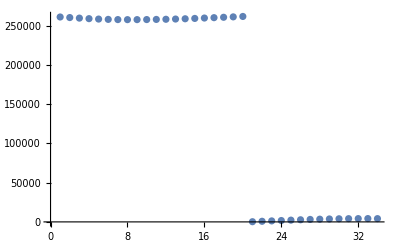

```mathematica
ListPlot[firIn]
```

```mathematica
firOut
```

{261154,260440,259729,259041,258514,258113,257860,257780,257805,257883,258056,258252,258548,258893,259321,259827,260301,260790,261309,261836,241,787,1268,1751,2247,2720,3144,3457,3740,3981,4122,4195,4234,4167}

```mathematica
LongestCommonSubsequence[ListConvolve[ker,firIn],firOut]
```

{}

```mathematica
s
```

```mathematica
TableForm[Join[{Range[Length[snaps]]},Transpose@snaps]];
```

```mathematica
rng=Range[#,#+3]&/@Range[1,5*3,3];
```

```mathematica
(*(Drop[ShiftRight[snaps[[#1]],1]+(snaps[[#2]]*snaps[[#3]]),-4]==Drop[snaps[[#4]],4])&@@@rng*)
```

### Upsampling:

```mathematica
upker={0.004349354184333842,-0.012460526975242473,-0.04179305187785534,0.11580155515788863,0.4377645703903624,0.4377645703903624,0.11580155515788867,-0.04179305187785537,-0.012460526975242473,0.004349354184333842};
```

```mathematica
f=0.113;
```

```mathematica
in=Sin[2*π*f*#]&/@Range[100];
```

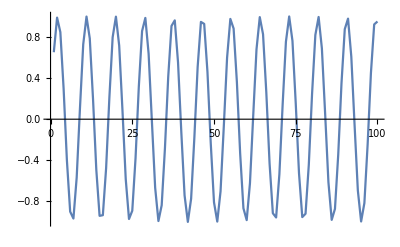

```mathematica
ListPlot[in,Joined->True]
```

```mathematica
inR=Flatten@Riffle[in,0];
```

```mathematica
out=ListConvolve[fupker/2^16,inR,1,0];
```

```mathematica
LinInt[list_]:=Module[{i,intlist={}},For[i=1,i< Length[list],i++,AppendTo[intlist,list[[i]]];LargeAppendTo[intlist,(list[[i]]+list[[i+1]])/2]];AppendTo[intlist,Last[list]];AppendTo[intlist,2*Last[intlist]-intlist[[-2]]];intlist]
```

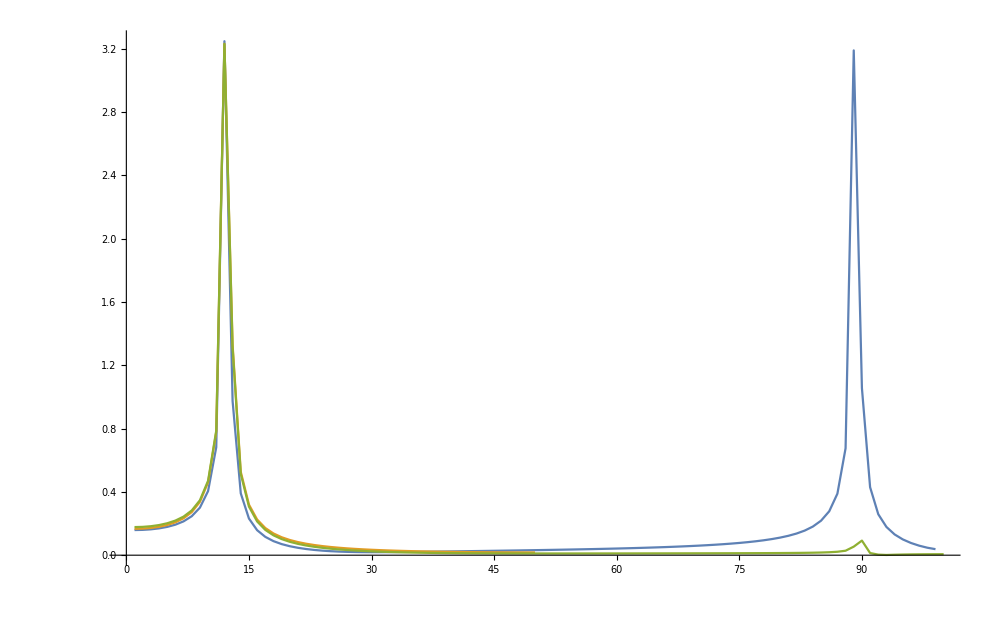

```mathematica
ListPlot[{Half@Abs[Fourier[inR]],(Half@Abs@Fourier@in)/1.345,(Half@Abs@Fourier@LinInt@in)/1.85},Joined->True,PlotRange->All,ImageSize->1000]
```

```mathematica
Manipulate[ListPlot[Abs@Fourier@Flatten@Riffle[Sin[2*π*f*#]&/@Range[100],{{0,0}}],Joined->True,ImageSize->300,PlotRange->{0,3}],{f,0,0.5,0.01}]
```

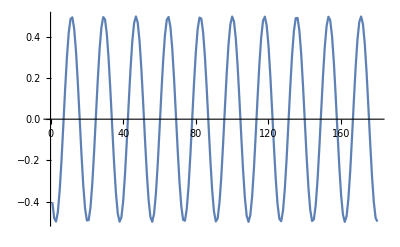

```mathematica
ListPlot[out,Joined->True]
```